```mathematica
<<peeters`
peeters`setGitDir["../project/figures/phy452-basicstatmech"]

"peeters`"
```

peeters`

/Users/pjoot/project/figures/phy452-basicstatmech

peeters`

```mathematica
<<MaTeX`
SetOptions[MaTeX,"Preamble"->{"\\usepackage{xcolor,txfonts}","\\definecolor{BlueDarker}{HTML}{0000AA}","\\definecolor{RedDarker}{HTML}{AA0000}","\\definecolor{PurpleDarker}{HTML}{550055}","\\definecolor{OrangeDarker}{HTML}{AA5500}","\\definecolor{GreenDarker}{HTML}{00AA00}"},
"FontSize" -> 18];
```

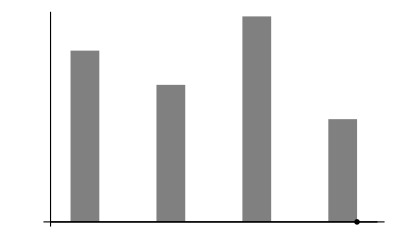

```mathematica
(*Plot[-x^2, {x, -1, 1}, Axes -> None, PlotRange -> {-1, 0.5}]*)



basicStatMechLecture2Fig1 = BarChart[{ 5, 4, 6, 3}, BarSpacing -> 2, Ticks->None,
ChartStyle->{{ Gray},  EdgeForm[Thickness[0]] }, AxesLabel-> {MaTeX["x"], MaTeX["P(x)"]}]
```

```mathematica
peeters`exportForLatex["basicStatMechLecture2Fig1",basicStatMechLecture2Fig1 ]
```

{basicStatMechLecture2Fig1.eps,basicStatMechLecture2Fig1pn.png}

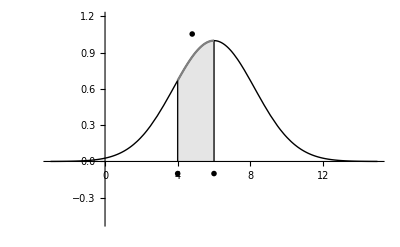

```mathematica
f[x_] := Exp[-(x-6)^2/10]
p1 = Plot[f[x],{x,-3,15} ,Ticks->None,PlotStyle->{Thick, Black},
AxesLabel-> {MaTeX["x"], MaTeX["P(x)"]}, PlotRange-> {{-3,15},{-0.5,1.2}}
];
x0 = 4;
x1 = 6;
p2 = Plot[f[x],{x,x0,x1}, Filling -> Bottom, PlotRange -> {{4,6},{0,1}}
,Ticks->None,PlotStyle->Gray
];

basicStatMechLecture2Fig2 = Show[{
p1, 
p2, 
Graphics[{
Black,
Line[{{x0, 0}, {x0,f[x0]}}],
Line[{{x1, 0}, {x1,f[x1]}}],
Text[ MaTeX["x_0"],{x0,-0.1} ],
Text[ MaTeX["x_1"], {x1, -0.1}],
Text[ MaTeX["\\Delta x"], {(x1 + x0)/2-0.2, f[(x1 + x0)/2] + 0.15}]
}]
}]
```

```mathematica
peeters`exportForLatex["basicStatMechLecture2Fig2",basicStatMechLecture2Fig2 ]
```

{basicStatMechLecture2Fig2.eps,basicStatMechLecture2Fig2pn.png}

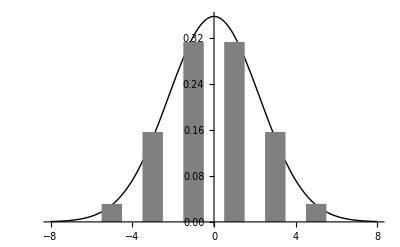

{-5,-3,-1,1,3,5}

{-7,-5,-3,-1,1,3,5,7}

```mathematica
ClearAll[pn, pmatchQ]
(*pmatchQ[x_, n_] := (EvenQ[x] && EvenQ[n]) || (OddQ[x] && OddQ[n])*)
pmatchQ[x_, n_] := (EvenQ[x] == EvenQ[n])
pn[x_, n_] := (1/2)^n Factorial[n]/Factorial[(n-x)/2]/Factorial[(n+x)/2]*Boole[pmatchQ[x,n]]

ClearAll[basicStatMechLecture2Fig9, pnc, f2, rect, odds]

odds[n_] := 2*(Range[n]-n/2)-1;
(*f = BarChart[pn[#, 5]&/@ odds[6] , BarSpacing -> 2, Ticks->None,
ChartStyle->{{ Gray},  EdgeForm[Thickness[0]] }, Axes -> None ];*)
pnc[x_, n_] := (2/Sqrt[2  Pi n ]) Exp[ -(x)^2/2/n]
f2 = Plot[pnc[x, 5], {x,-8,8}, 
Ticks -> None, 
PlotStyle-> {Thick, Black},
AxesLabel-> {MaTeX["x"], MaTeX["P(x)"]}];
rect[x_, n_] := Module[ {h}, h = pn[x, n]; Rectangle[{x-1/2, 0}, {x+1/2, h}] ]
basicStatMechLecture2Fig9 = Show[{
f2,
Graphics[{
Gray,
rect[#,5] &/@ odds[6]
}]
}]
```

```mathematica
peeters`exportForLatex["basicStatMechLecture2Fig9",basicStatMechLecture2Fig9 ]
```

{basicStatMechLecture2Fig9.eps,basicStatMechLecture2Fig9pn.png}